# nBEPA1 protocol: Limiting distribution and average hitting time in 2-strategy Single-Optimum Coordination Games

## Luis R. Izquierdo and Segismundo S. Izquierdo

## License

2s-SOCG-nBEPA1-LimitingDistribution-AvgHittingTime 
is a Mathematica notebook created to analyze the 
nBEPA1 protocol in 2-strategy Single-Optimum Coordination Games.
Copyright (C) 2021. Luis R. Izquierdo and Segismundo S. Izquierdo

This program is free software: you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  
See the GNU General Public License for more details.

You can find a copy of the GNU General Public License at https://www.gnu.org/licenses/gpl.html.

Contact information: 
Luis R. Izquierdo 
University of Burgos, Spain. 
website: http://luis.izqui.org

## Source code

```mathematica
LimitingDistributionAndAvgHittingTimeInTicks::usage="LimitingDistributionAndAvgHittingTimeInTicks[ n, noise, initialState, finalState] returns a list with information about the nBEPA1 protocol in a single-optimum coordination game with 2 strategies, where the second strategy is optimal (e.g. {{1,0},{0,2}}), played in a population context with n agents. The output list has two elements:
- The first element is the exact limiting distribution. This is list with (n+1) elements, where the i-th element is the long-run probability that the process is at the state where there are exactly i-1 agents using strategy 2.
- The second element is the exact average hitting time from initial state initialState to final state finalState, in ticks, where a tick is the lapse of time over which every agent is expected to receive one revision opportunity.

PARAMETERS:
- n is the population size, i.e. the number of agents in the population.
- noise is the noise in the nBEPA1 protocol, i.e. the probability that the revising agent chooses a strategy at random. It must be a number strictly greater than 0 and no greater than 1.
- initialState is the number of agents using strategy 2 at the initial state used to compute the average hitting time. It must be an integer in the interval [0, n].
- finalState is the number of agents using strategy 2 at the final state used to compute the average hitting time. It must be an integer in the interval [0, n]." ;

LimitingDistributionAndAvgHittingTimeInTicks[n_,noise_,initialState_,finalState_]:=Module[{μ,avgHittingTime,p,q,list},
(* Game: {{1,0},{0,2}}. x is the proportion of 2-strategists *)
(* Protocol: nBEPA1 = {BEP, Test All, one trial, and noise} *)

(* Probability of increasing the number of 2-strategists by one *)
(* P(revising agent is a 1-strategist)=(1-x) *)
(* It will change if it meets a 2-strategist when testing strategy 2: (xn)/(n-1) 
and with probability 1/2 if there is miscoordination: (xn/(n-1)) (((1-x)n-1)/(n-1))/2 *)
p[x_]:=(1-x)*((1-noise)* ((x n/(n-1))+(x n/(n-1))(((1-x)n-1)/(n-1))/2)+noise/2);

(* Probability of decreasing the number of 2-strategists by one *)
(* P(revising agent is a 2-strategist)=x *)
(* It will change if it meets a 1-strategist when testing both strategies: ((1-x)n/(n-1))^2 
and with probability 1/2 if there is miscoordination: (((1-x)n)/(n-1))((xn-1)/(n-1))/2 *)
q[x_]:=x ((1-noise)(((1-x) n/(n-1))^2+((1-x) n)/(n-1)((x n-1)/(n-1))/2)+noise/2);

(* Limiting distribution *)
(* Sandholm 2010, p.404, eq 11.11 *)
μ=Normalize[FoldList[Times,1,Table[p[(j-1)/n]/q[j/n],{j,n}]],Total];

(* Average hitting time *)
If[initialState<finalState,
(* initial state has a lower proportion of 2-strategists than final state *)
(* Sandholm 2010, p.439, eq 11.44 *)
list=Table[q[i/n]/p[i/n],{i,n-1}];
avgHittingTime=Sum[Sum[Times@@list[[j;;k-1]]/p[(j-1)/n],{j,1,k}],{k,initialState+1,finalState}]
,
(* final state has a lower proportion of 2-strategists than initial state *)
(* Sandholm 2010, p.439, eq 11.45 *)
list=Table[p[i/n]/q[i/n],{i,n-1}];
avgHittingTime=Sum[Sum[Times@@list[[k;;j-1]]/q[j/n],{j,k,n}],{k,finalState+1,initialState}]
];

(* We divide avgHittingTime by n so the unit of time is the lapse of time over which every agent is expected to receive one revision opportunity, aka a tick *)
{μ,avgHittingTime/n}
]
```

## Examples of usage

### Instructions

```mathematica
?LimitingDistributionAndAvgHittingTimeInTicks
```

### Figure 4 in “Decentralized, Fast and Scalable Almost-Global Convergence in Single-Optimum Coordination Problems”, by Izquierdo, Izquierdo and Rodríguez

Long-run fraction of time  μ^(N,ϵ=0.001)(e_1) spent at inefficient state e_1 (in orange) and average hitting time of e_1 from state x=(0.9,0.1) (in blue), for the nBEPA1 protocol in the 2-strategy single-optimum coordination game with payoff matrix {{1,0},{0,2}}, for various population sizes

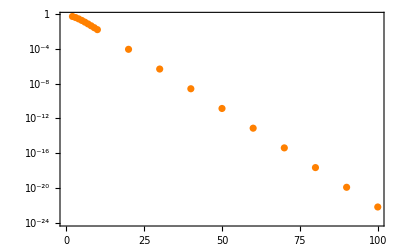
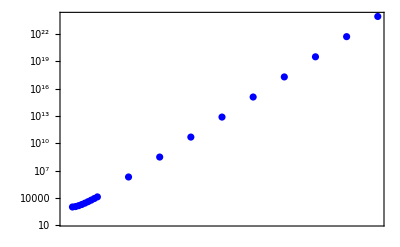

| N | Fraction of time at e_1 | Avg. hitting time
 | 2 | 0.49975 | 1001.
 | 3 | 0.374563 | 1113.19
 | 4 | 0.262734 | 1403.07
 | 5 | 0.174702 | 1889.61
 | 6 | 0.11164 | 2652.45
 | 7 | 0.0694115 | 3830.52
 | 8 | 0.0423895 | 5647.69
 | 9 | 0.0255964 | 8459.54
 | 10 | 0.0153492 | 12830.
 | 20 | 0.0000844565 | 1.98258×10^6
 | 30 | 4.58665×10^-7 | 3.07318×10^8
 | 40 | 2.49548×10^-9 | 4.80753×10^10
 | 50 | 1.35974×10^-11 | 7.59776×10^12
 | 60 | 7.41778×10^-14 | 1.21298×10^15
 | 70 | 4.05054×10^-16 | 1.9553×10^17
 | 80 | 2.21365×10^-18 | 3.18035×10^19
 | 90 | 1.21063×10^-20 | 5.21564×10^21
 | 100 | 6.62493×10^-23 | 8.6174×10^23

```mathematica
noise= 10^-3;
listOfPopulations=Join[Range[2,9],Range[10,100,10]];
initialState[n_]:=n-Floor[0.9n];
finalState=0;

l=Table[{n,LimitingDistributionAndAvgHittingTimeInTicks[n,noise,initialState[n],finalState]},{n,listOfPopulations}];

(* Only interested in the fraction of time spent at final state 0, i.e. the first state *)
fractionOfTimeAtFinalState=Map[{First[#],N@First[First[Last[#]]]}&,l];
avgHittingTime=Map[{First[#],N@Last[Last[#]]}&,l];

(* Actual plot *)
Overlay[{
ListLogPlot[fractionOfTimeAtFinalState,PlotStyle->Orange,ImagePadding->{{40,30},{20,10}},Frame->{True,True,True,False},FrameStyle->{Automatic,Orange,Automatic,Automatic}],
ListLogPlot[avgHittingTime,PlotStyle->Blue,ImagePadding->{{40,30},{20,10}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Blue}]}]
(* Table *)
TableForm[Append[fractionOfTimeAtFinalStateᵀ,Last[avgHittingTimeᵀ]]ᵀ,TableHeadings->{{},{"N","Fraction of time at e_1","Avg. hitting time"}},TableAlignments->Center]
```

### Figure 5 in “Decentralized, Fast and Scalable Almost-Global Convergence in Single-Optimum Coordination Problems”, by Izquierdo, Izquierdo and Rodríguez

Long-run fraction of time  μ^(N=50,ϵ)(e_1) spent at inefficient state e_1 (in orange) and average hitting time of e_1 from state x=(0.9,0.1) (in blue), for the nBEPA1 protocol in the 2-strategy single-optimum coordination game with payoff matrix {{1,0},{0,2}}, for various noise levels

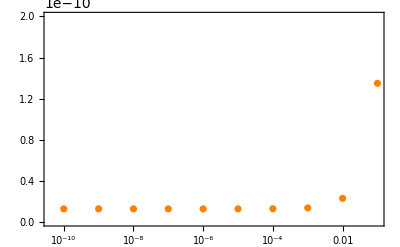
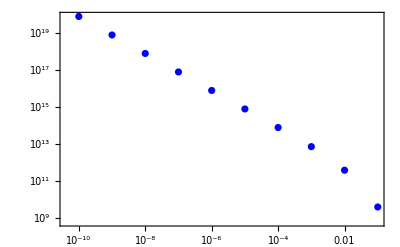

| Noise | Fraction of time at e_1 | Avg. hitting time
 | 1.×10^-10 | 1.26873×10^-11 | 8.25547×10^19
 | 1.×10^-9 | 1.26873×10^-11 | 8.25547×10^18
 | 1.×10^-8 | 1.26873×10^-11 | 8.25546×10^17
 | 1.×10^-7 | 1.26874×10^-11 | 8.2554×10^16
 | 1.×10^-6 | 1.26882×10^-11 | 8.25477×10^15
 | 0.00001 | 1.26963×10^-11 | 8.24849×10^14
 | 0.0001 | 1.27771×10^-11 | 8.18606×10^13
 | 0.001 | 1.35974×10^-11 | 7.59776×10^12
 | 0.01 | 2.29134×10^-11 | 4.03495×10^11
 | 0.1 | 1.34922×10^-10 | 4.15825×10^9

```mathematica
n=50;
listOfNoises=10^Range[-10,-1];
initialState[n_]:=n-Floor[0.9n];
finalState=0;

l=Table[{noise,LimitingDistributionAndAvgHittingTimeInTicks[n,noise,initialState[n],finalState]},{noise,listOfNoises}];

(* Only interested in the fraction of time spent at final state 0, i.e. the first state *)
fractionOfTimeAtFinalState=Map[{First[#],N@First[First[Last[#]]]}&,l];
avgHittingTime=Map[{First[#],N@Last[Last[#]]}&,l];

(* Actual plot *)
Overlay[{
ListLogLinearPlot[fractionOfTimeAtFinalState,PlotStyle->Orange,ImagePadding->{{60,30},{20,10}},Frame->{True,True,True,False},FrameStyle->{Automatic,Orange,Automatic,Automatic},PlotRange->{0,2*10^-10}],
ListLogLogPlot[avgHittingTime,PlotStyle->Blue,ImagePadding->{{60,30},{20,10}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Blue}]}]
(* Table *)
TableForm[Append[N@fractionOfTimeAtFinalStateᵀ,Last[avgHittingTimeᵀ]]ᵀ,TableHeadings->{{},{"Noise","Fraction of time at e_1","Avg. hitting time"}},TableAlignments->Center]
```

### Figure 6 in “Decentralized, Fast and Scalable Almost-Global Convergence in Single-Optimum Coordination Problems”, by Izquierdo, Izquierdo and Rodríguez

Long-run fraction of time  μ^(N,ϵ=0.001)(O_0.01(e_2)) spent in the neighborhood O_0.01(e_2) (in orange) and average hitting time of the same neighborhood from state x=(0.9,0.1) (in blue), for the nBEPA1 protocol in the 2-strategy single-optimum coordination game with payoff matrix {{1,0},{0,2}}, for various population sizes

General::munfl: 1./(2.43487055703981×10^338) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.750375/(2.43487055703981×10^338) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.844563/(2.43487055703981×10^338) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1./(6.41217443477377×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.70035/(6.41217443477377×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.770771/(6.41217443477377×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

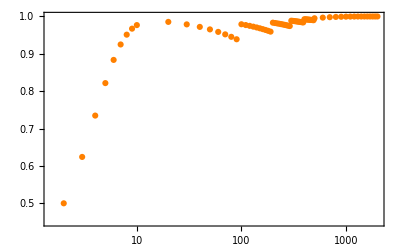
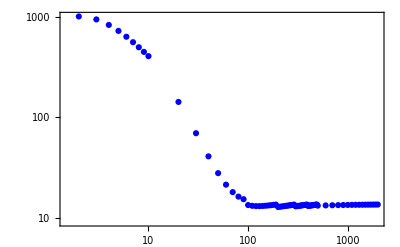

| N | Fraction of time at Neighborhood | Avg. hitting time
 | 2 | 0.49975 | 1001.
 | 3 | 0.623939 | 935.788
 | 4 | 0.734639 | 825.059
 | 5 | 0.821585 | 719.711
 | 6 | 0.883668 | 630.019
 | 7 | 0.925027 | 556.035
 | 8 | 0.951264 | 495.41
 | 9 | 0.967328 | 445.565
 | 10 | 0.97688 | 404.268
 | 20 | 0.985456 | 142.119
 | 30 | 0.978789 | 69.5506
 | 40 | 0.972051 | 41.0008
 | 50 | 0.965348 | 27.9381
 | 60 | 0.958686 | 21.4668
 | 70 | 0.952068 | 18.1158
 | 80 | 0.945495 | 16.3438
 | 90 | 0.938966 | 15.4076
 | 100 | 0.979128 | 13.4794
 | 110 | 0.976998 | 13.2499
 | 120 | 0.97485 | 13.1641
 | 130 | 0.972685 | 13.1601
 | 140 | 0.970503 | 13.2024
 | 150 | 0.968305 | 13.2706
 | 160 | 0.966091 | 13.3528
 | 170 | 0.963861 | 13.4419
 | 180 | 0.961616 | 13.5338
 | 190 | 0.959355 | 13.6261
 | 200 | 0.983339 | 12.8978
 | 210 | 0.982391 | 12.9858
 | 220 | 0.98143 | 13.0716
 | 230 | 0.980457 | 13.1551
 | 240 | 0.979472 | 13.2362
 | 250 | 0.978474 | 13.3148
 | 260 | 0.977465 | 13.3912
 | 270 | 0.976443 | 13.4654
 | 280 | 0.97541 | 13.5374
 | 290 | 0.974364 | 13.6074
 | 300 | 0.98861 | 13.0918
 | 310 | 0.988126 | 13.1571
 | 320 | 0.987634 | 13.2206
 | 330 | 0.987135 | 13.2825
 | 340 | 0.986629 | 13.3429
 | 350 | 0.986116 | 13.4017
 | 360 | 0.985595 | 13.4592
 | 370 | 0.985066 | 13.5153
 | 380 | 0.984531 | 13.5701
 | 390 | 0.983988 | 13.6237
 | 400 | 0.992548 | 13.2196
 | 410 | 0.992283 | 13.2703
 | 420 | 0.992013 | 13.3199
 | 430 | 0.99174 | 13.3685
 | 440 | 0.991462 | 13.4161
 | 450 | 0.991179 | 13.4628
 | 460 | 0.990893 | 13.5086
 | 470 | 0.990601 | 13.5535
 | 480 | 0.990306 | 13.5976
 | 490 | 0.990006 | 13.6409
 | 500 | 0.995205 | 13.3074
 | 600 | 0.996936 | 13.3714
 | 700 | 0.998048 | 13.4201
 | 800 | 0.998758 | 13.4585
 | 900 | 0.99921 | 13.4896
 | 1000 | 0.999497 | 13.5153
 | 1100 | 0.99968 | 13.5369
 | 1200 | 0.999796 | 13.5553
 | 1300 | 0.99987 | 13.5711
 | 1400 | 0.999917 | 13.585
 | 1500 | 0.999947 | 13.5972
 | 1600 | 0.999966 | 13.6079
 | 1700 | 0.999978 | 13.6176
 | 1800 | 0.999986 | 13.6262
 | 1900 | 0.999991 | 13.6341
 | 2000 | 0.999994 | 13.6412

```mathematica
noise= N[10^-3]; (* Here we include N[] to make computations run (way faster) in floating-point airthmetic, rather than rational arithmetic. For exact results, remove N[] *) 
listOfPopulations=Join[Range[2,9],Range[10,490,10],Range[500,2000,100]];
initialState[n_]:=n-Floor[0.9n];
Clear[finalState];
finalState[n_]:=n-Floor[0.01 n];

l=ParallelTable[{n,LimitingDistributionAndAvgHittingTimeInTicks[n,noise,initialState[n],finalState[n]]},{n,listOfPopulations}] ;

(* Only interested in the fraction of time spent at a small neighborhood around the last state (i.e. n+1). To be precise: Total[μ[[(n+1)-Floor[0.01 n];;]]] *)
fractionOfTimeAtNbrhood=Map[{First[#],N@Total[(First[Last[#]])[[First[#]+1-Floor[0.01 First[#]];;]]]}&,l];
avgHittingTime=Map[{First[#],N@Last[Last[#]]}&,l];

(* Actual plot *)
Overlay[{
ListLogLinearPlot[fractionOfTimeAtNbrhood,PlotStyle->Orange,ImagePadding->{{30,30},{20,10}},Frame->{True,True,True,False},FrameStyle->{Automatic,Orange,Automatic,Automatic},PlotRange->{0.45,1}],
ListLogLogPlot[avgHittingTime,PlotStyle->Blue,ImagePadding->{{30,30},{20,10}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Blue}]}]
(* Table *)
TableForm[Append[fractionOfTimeAtNbrhoodᵀ,Last[avgHittingTimeᵀ]]ᵀ,TableHeadings->{{},{"N","Fraction of time at Neighborhood","Avg. hitting time"}},TableAlignments->Center]
```

#### Statement: “For any N>=100, μ^(N,ϵ=0.001)(O_0.01(e_2))>0.95 and the average hitting time is less than 14 ticks, i.e. it takes on average less than 14 revisions per agent to reach the neighborhood O_0.01(e_2), and the process spends more than 95% of the time in that neighborhood.”

```mathematica
listOfPopulations=Range[199,2000,100];

l=ParallelTable[{n,LimitingDistributionAndAvgHittingTimeInTicks[n,noise,initialState[n],finalState[n]]},{n,listOfPopulations}] ;

(* Only interested in the fraction of time spent at a small neighborhood around the last state (i.e. n+1). To be precise: Total[μ[[(n+1)-Floor[0.01 n];;]]] *)
fractionOfTimeAtNbrhood=Map[{First[#],N@Total[(First[Last[#]])[[First[#]+1-Floor[0.01 First[#]];;]]]}&,l];
avgHittingTime=Map[{First[#],N@Last[Last[#]]}&,l];

(* Table *)
TableForm[Append[fractionOfTimeAtNbrhoodᵀ,Last[avgHittingTimeᵀ]]ᵀ,TableHeadings->{{},{"N","Fraction of time at Neighborhood","Avg. hitting time"}},TableAlignments->Center]
```

General::munfl: 1./(1.44771305294673×10^338) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.749875/(1.44771305294673×10^338) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.843813/(1.44771305294673×10^338) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1./(3.81249431307576×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.69985/(3.81249431307576×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.770045/(3.81249431307576×10^315) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1./(2.08403695705563×10^383) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.849925/(2.08403695705563×10^383) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.998855/(2.08403695705563×10^383) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1./(2.99483131357515×10^428) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.949975/(2.99483131357515×10^428) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.16391/(2.99483131357515×10^428) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| N | Fraction of time at Neighborhood | Avg. hitting time
 | 199 | 0.957308 | 13.6955
 | 299 | 0.973413 | 13.6608
 | 399 | 0.983493 | 13.665
 | 499 | 0.989732 | 13.6745
 | 599 | 0.993594 | 13.6842
 | 699 | 0.995991 | 13.6929
 | 799 | 0.997484 | 13.7005
 | 899 | 0.998417 | 13.7071
 | 999 | 0.999001 | 13.7129
 | 1099 | 0.999369 | 13.718
 | 1199 | 0.9996 | 13.7224
 | 1299 | 0.999746 | 13.7263
 | 1399 | 0.999839 | 13.7298
 | 1499 | 0.999897 | 13.733
 | 1599 | 0.999935 | 13.7358
 | 1699 | 0.999958 | 13.7384
 | 1799 | 0.999973 | 13.7407
 | 1899 | 0.999983 | 13.7428
 | 1999 | 0.999989 | 13.7448

The trajectory hits the neighborhood O at time 13.789

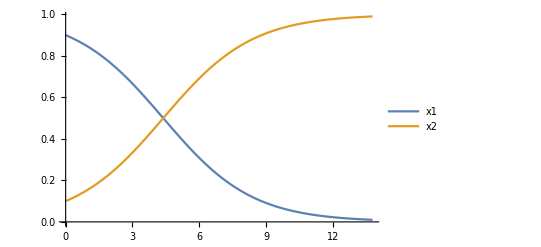

```mathematica
(* Here we check the limit of the hitting time when the population is large, using the Mean Dynamic *)
Clear["Global`*"];

(* Mean Dynamic for nBEPA1 in the 2-strategy SOCG *)
s=2; (* 2 strategies *)
noise=10^-3;
MD=(1-noise)*{x1[t]^2+(x1[t] x2[t])/2 ,x2[t]+(x1[t] x2[t])/2}+noise{1/2,1/2}-{x1[t],x2[t]};

initialPoint={0.9,0.1};

(*NDSolve*)
sol=NDSolveValue[
{{x1'[t],x2'[t]}==MD,{x1[0],x2[0]}==initialPoint,
WhenEvent[x2[t]>=1-0.01, "StopIntegration";hittingTime=t]},
{x1[t],x2[t]},{t,0,100},AccuracyGoal->12];

Print["The trajectory hits the neighborhood O at time ", hittingTime];
Plot[Evaluate@MapThread[Tooltip,{sol,{x1,x2}}],{t,0,hittingTime},PlotLegends->{x1,x2}]
```